```mathematica
randomi1 = RandomInteger[{1,2^2}]
randomi2 = RandomInteger[{1,2^3}]
randomi3 = RandomInteger[{1,2^2}]
randomi4 = RandomInteger[{1,2^3}]
randomk = RandomInteger[{1,2^3}]
```

4

5

4

1

1

```mathematica
g=NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,1,1,1}],
{left___,1,0,s___}:>Flatten[{left,s,0,0,1}],
{left___,0,1,s___}:>Flatten[{left,s,1,1,0}],
{left___,1,1,s___}:>Flatten[{left,s,0,1,1}]

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi4]]}]*)

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]*)
}],
{{0,0,1}},
(*{Tuples[{0,1},l][[randomk]]},*)
(*{Tuples[{0,1},l][[k]]},*)
5,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]
With[{vertices=VertexList[g]},HighlightGraph[g,Style[PathGraph[FindShortestPath[g,First[VertexList[g]],vertices[[Length[vertices]]]],DirectedEdges->True],Red]]]
```

-Graphics-

-Graphics-

```mathematica
allPaths = FindPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]],Infinity,All]
Table[Length /@allPaths[[i]],{i,1,Length[allPaths]}]
Length /@FindPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]],Infinity,All][[3]]
```

{{{0,1,1},{1,1,0},{1,0,1,0},{1,0,0,1,0},{1,0,0,0,1,0},{1,0,0,0,0,1,0}},{{0,1,1},{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,1,1,0},{1,0,1,0},{1,0,0,1,0},{1,0,0,0,1,0},{1,0,0,0,0,1,0}},{{0,1,1},{0,0,0,0},{0,0,0,1},{0,0,1,0},{1,0,0,1},{1,0,1,0},{1,0,0,1,0},{1,0,0,0,1,0},{1,0,0,0,0,1,0}},{{0,1,1},{1,1,0},{0,0,0,0},{0,0,0,1},{0,1,0,1},{0,1,1,0},{1,0,1,0},{1,0,0,1,0},{1,0,0,0,1,0},{1,0,0,0,0,1,0}},{{0,1,1},{1,1,0},{0,0,0,0},{0,0,0,1},{0,0,1,0},{1,0,0,1},{1,0,1,0},{1,0,0,1,0},{1,0,0,0,1,0},{1,0,0,0,0,1,0}}}

{{3,3,4,5,6,7},{3,4,4,4,4,4,5,6,7},{3,4,4,4,4,4,5,6,7},{3,3,4,4,4,4,4,5,6,7},{3,3,4,4,4,4,4,5,6,7}}

{3,4,4,4,4,4,5,6,7}

```mathematica
Length /@FindShortestPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]]]
```

{3,4,5,6,7,8}

```mathematica
(*Dependencies*)
AllPathCanyonsBinary[g_]:=Style[Text[
With[
{
vertices=VertexList[g]
(*,randomInit=Tuples[{0,1},2]*)
,allPaths = FindPath[g,First[VertexList[g]],VertexList[g][[Length[VertexList[g]]]],Infinity,All]
},
(*Length /@FindShortestPath[g,First[VertexList[g]],vertices[[Length[vertices]]]]*)
 Length /@allPaths[[-1]]
]//.{x_}:>x]]

(*The default lFn function is run unless you specify something else! Does the AllPathCanyonsBinary function necessarily specify the conditions & rules of the tag system? No! *)
lFn[i1_,i2_,i3_,i4_,j_,k_,l_,t_]:= AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,0,0,1}],
{left___,1,0,s___}:>Flatten[{left,s,0,1,1}],
{left___,0,1,s___}:>Flatten[{left,s,0,1,1}],
{left___,1,1,s___}:>Flatten[{left,s,0,1,1}]

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi4]]}]*)

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]*)
}],
{{0,1,0}},
(*{Tuples[{0,1},l][[randomk]]},*)
(*{Tuples[{0,1},l][[k]]},*)
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
```

```mathematica
Table[Table[Table[Table[Table[Show[
ListStepPlot[
Legended[
lFn[i1,i2,i3,i4,j,k,l,t][[1]][[1]],
StringTemplate[
"{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->{0,0,1},
"b"->{0,1,1},
"c":>{0,1,1},
"d":>{0,1,1},
"e":>{0,1,0}


(*"a"->Tuples[{0,1},j][[randomi1]],
"b"->Tuples[{0,1},j][[randomi2]],
"c":>Tuples[{0,1},j][[randomi3]],
"d":>Tuples[{0,1},j][[randomi4]],
"e":>Tuples[{0,1},l][[randomk]]*)


(*"a"->Tuples[{0,1},j][[i1]],
"b"->Tuples[{0,1},j][[i2]],
"c":>Tuples[{0,1},j][[i3]],
"d":>Tuples[{0,1},j][[i4]],
"e":>Tuples[{0,1},l][[k]]*)
|>]
]]],{t,1,25}],
{i1,2^j,2^j},
{i2,2^j,2^j},
{i3,2^j,2^j},
{i4,2^j,2^j}],
{j,3,3}],
{k,2^l,2^l}],
{l,3,3}]/.{{{{{{{x_}}}}}}} -> x
```

$Aborted

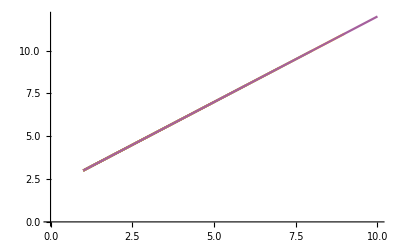

```mathematica
ListLinePlot[Table[Table[Table[Table[Table[
lFn[i1,i2,i3,i4,j,k,l,t][[1]][[1]]
,{t,1,9}],
{i1,2^j,2^j},
{i2,2^j,2^j},
{i3,2^j,2^j},
{i4,2^j,2^j}],
{j,3,3}],
{k,2^l,2^l}],
{l,3,3}]/.{{{{{{{x_}}}}}}} -> x]
```

```mathematica
lFn[i1_,i2_,i3_,i4_,j_,k_,l_,t_]:= AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{0,left___,left___,s___}:>{s,0,0},
{1,left___,left___,s___}:>{s,1,1,0,1}

(*{left___,0,0,s___}:>{left,s,0,0,0},
{left___,1,0,s___}:>{left,s,0,1,0},
{left___,0,1,s___}:>{left,s,1,0},
{left___,1,1,s___}:>{left,s,1,1,1}*)

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi4]]}]*)

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]*)
}],
(*{{1,0,1}},*)
(*{Tuples[{0,1},l][[randomk]]},*)
{Tuples[{0,1},l][[k]]},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
```

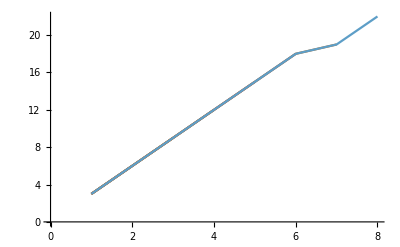

```mathematica
ListLinePlot[Table[Table[Table[Table[Table[
lFn[i1,i2,i3,i4,j,k,l,t][[1]][[1]]
,{t,1,7}],
{i1,2^j,2^j},
{i2,2^j,2^j},
{i3,2^j,2^j},
{i4,2^j,2^j}],
{j,3,3}],
{k,2^l,2^l}],
{l,3,3}]/.{{{{{{{x_}}}}}}} -> x]
```

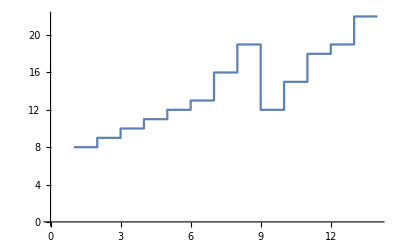

```mathematica
ListStepPlot[lFn[8,8,8,8,8,8,8,8][[1]][[1]]]
```

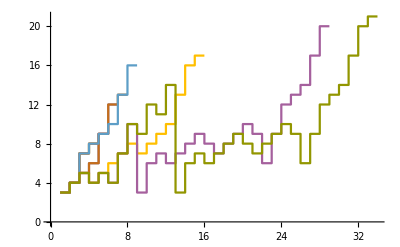

```mathematica
ListStepPlot[Table[Table[Table[Table[Table[
lFn[i1,i2,i3,i4,j,k,l,t][[1]][[1]]
,{t,1,10}],
{i1,2^j ,2^j},
{i2,2^j ,2^j},
{i3,2^j ,2^j},
{i4,2^j ,2^j}],
{j,3,3}],
{k,2^l,2^l}],
{l,3,3}]/.{{{{{{{x_}}}}}}} -> x]
```

```mathematica
lFn[r1_,r2_,r3_,r4_,init_,t_]:= AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,r1}],
{left___,1,0,s___}:>Flatten[{left,s,r2}],
{left___,0,1,s___}:>Flatten[{left,s,r3}],
{left___,1,1,s___}:>Flatten[{left,s,r4}]
}],
{init},
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]
```

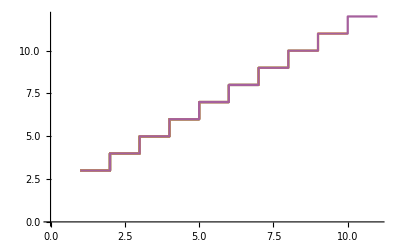

```mathematica
ListStepPlot[Table[Table[Table[Table[Table[
lFn[{0,0,1},{0,1,1},{0,1,1},{0,1,1},{0,1,0},t][[1]][[1]]
,{t,1,9}],
{i1,2^j,2^j},
{i2,2^j,2^j},
{i3,2^j,2^j},
{i4,2^j,2^j}],
{j,3,3}],
{k,1,2^l}],
{l,1,3}]/.{{{{{{{x_}}}}}}} -> x]
```